Para graficar regiones complejas usamos ComplexRegionPlot.

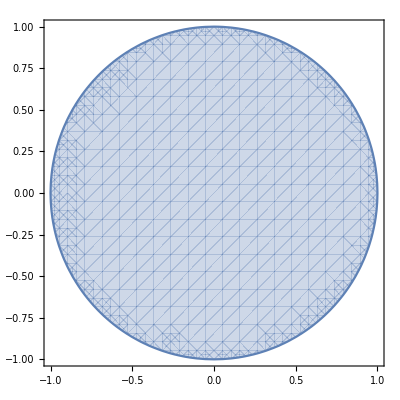

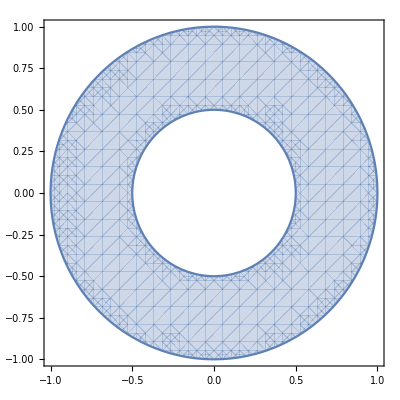

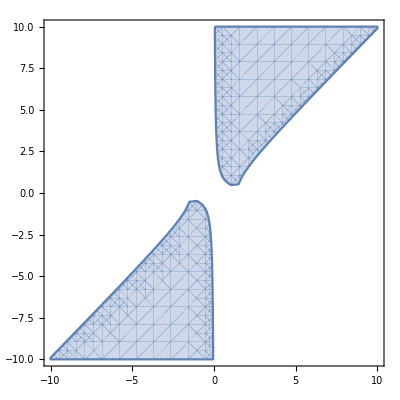

```mathematica
ComplexRegionPlot[Abs[z] <= 1, {z, -1 - I, 1 + I}]
ComplexRegionPlot[1/2<=Abs[z] <= 1, {z, -1 - I, 1 + I}]
ComplexRegionPlot[Re[z^2]<=2 && Im[z^2]>1, {z, -10 - 10I, 10 + 10I}]
```

Ahora con ayuda de la función ParametricPlot podemos definir un par de funciones
que nos muestran cómo se deforma el plano bajo un mapeo conforme mediante
mapeos polares y cartesianos.

```mathematica
polarMap[func_,radial_,polar_,options___]:=ParametricPlot[Evaluate[Through[{Re,Im}[func]]],radial,polar,options];
cartesianMap[func_,xrange_,yrange_,options___]:=ParametricPlot[Evaluate[Through[{Re,Im}[func]]],xrange,yrange,options];
```

```mathematica
polarConformal[func_,radial_,polar_,options___]:=Show[GraphicsGrid[{{polarMap[r Exp[I t],radial,polar,options, DisplayFunction->Identity],polarMap[func,radial,polar,options,DisplayFunction->Identity]}},{}],DisplayFunction -> $DisplayFunction]
cartesianConformal[func_,xrange_,yrange_,options___]:=Show[GraphicsGrid[{{cartesianMap[x+I*y,xrange,yrange,options, DisplayFunction->Identity],cartesianMap[w[x+I*y],xrange,yrange,options,DisplayFunction->Identity]}},{}],DisplayFunction -> $DisplayFunction]
```